# Manifold at q=4 cycles

## Solver

Solver to identify the coefficients with respect to the free parameter

## Coefficient polynomial structure

```mathematica
ClearAll[alpha,beta,gamma1,gamma2,gamma3,gamma4,gamma5,gamma6,a1,a2,a3,b1,b2];
alpha[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},(1/12) a1^2 b1-(1/12) a1 a2 b1-(1/12) a1 a3 b1-(1/24) a2^2 b1-(1/12) a2 a3 b1-(1/24) a3^2 b1+(1/12) a1^2 b2+(1/6) a1 a2 b2-(1/12) a1 a3 b2+(1/12) a2^2 b2-(1/12) a2 a3 b2-(1/24) a3^2 b2]
beta[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},-(1/24) a1 b1^2+(1/12) a2 b1^2+(1/12) a3 b1^2-(1/12) a1 b1 b2-(1/12) a2 b1 b2+(1/6) a3 b1 b2-(1/24) a1 b2^2-(1/24) a2 b2^2+(1/12) a3 b2^2]
gamma1[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},-1.38889*10^-3*a1^4*b1-5.55556*10^-3*a1^3*a2*b1-5.55556*10^-3*a1^3*a3*b1+2.08333*10^-3*a1^2*a2^2*b1+4.16667*10^-3*a1^2*a2*a3*b1+2.08333*10^-3*a1^2*a3^2*b1+4.86111*10^-3*a1*a2^3*b1+1.45833*10^-2*a1*a2^2*a3*b1+1.45833*10^-2*a1*a2*a3^2*b1+4.86111*10^-3*a1*a3^3*b1+1.21528*10^-3*a2^4*b1+4.86111*10^-3*a2^3*a3*b1+7.29167*10^-3*a2^2*a3^2*b1+4.86111*10^-3*a2*a3^3*b1+1.21528*10^-3*a3^4*b1-1.38889*10^-3*a1^4*b2-5.55556*10^-3*a1^3*a2*b2-5.55556*10^-3*a1^3*a3*b2-8.33333*10^-3*a1^2*a2^2*b2-1.66667*10^-2*a1^2*a2*a3*b2+2.08333*10^-3*a1^2*a3^2*b2-5.55556*10^-3*a1*a2^3*b2-1.66667*10^-2*a1*a2^2*a3*b2+4.16667*10^-3*a1*a2*a3^2*b2+4.86111*10^-3*a1*a3^3*b2-1.38889*10^-3*a2^4*b2-5.55556*10^-3*a2^3*a3*b2+2.08333*10^-3*a2^2*a3^2*b2+4.86111*10^-3*a2*a3^3*b2+1.21528*10^-3*a3^4*b2]
gamma2[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},-8.33333*10^-3*a1^3*b1^2+6.25000*10^-3*a1^2*a2*b1^2+6.25000*10^-3*a1^2*a3*b1^2+1.04167*10^-3*a1*a2^2*b1^2+2.08333*10^-3*a1*a2*a3*b1^2+1.04167*10^-3*a1*a3^2*b1^2+2.08333*10^-3*a2^3*b1^2+6.25000*10^-3*a2^2*a3*b1^2+6.25000*10^-3*a2*a3^2*b1^2+2.08333*10^-3*a3^3*b1^2-1.66667*10^-2*a1^3*b1*b2-8.33333*10^-3*a1^2*a2*b1*b2+1.25000*10^-2*a1^2*a3*b1*b2+1.25000*10^-2*a1*a2^2*b1*b2+4.16667*10^-3*a1*a2*a3*b1*b2+2.08333*10^-3*a1*a3^2*b1*b2+4.16667*10^-3*a2^3*b1*b2+2.08333*10^-3*a2^2*a3*b1*b2+2.08333*10^-3*a2*a3^2*b1*b2+4.16667*10^-3*a3^3*b1*b2-8.33333*10^-3*a1^3*b2^2-2.50000*10^-2*a1^2*a2*b2^2+6.25000*10^-3*a1^2*a3*b2^2-2.50000*10^-2*a1*a2^2*b2^2+1.25000*10^-2*a1*a2*a3*b2^2+1.04167*10^-3*a1*a3^2*b2^2-8.33333*10^-3*a2^3*b2^2+6.25000*10^-3*a2^2*a3*b2^2+1.04167*10^-3*a2*a3^2*b2^2+2.08333*10^-3*a3^3*b2^2]
gamma3[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},2.77778*10^-3*a1^3*b1^2-1.25000*10^-2*a1^2*a2*b1^2-1.25000*10^-2*a1^2*a3*b1^2+8.33333*10^-3*a1*a2^2*b1^2+1.66667*10^-2*a1*a2*a3*b1^2+8.33333*10^-3*a1*a3^2*b1^2+2.77778*10^-3*a2^3*b1^2+8.33333*10^-3*a2^2*a3*b1^2+8.33333*10^-3*a2*a3^2*b1^2+2.77778*10^-3*a3^3*b1^2+5.55556*10^-3*a1^3*b1*b2-4.16667*10^-3*a1^2*a2*b1*b2-2.50000*10^-2*a1^2*a3*b1*b2-1.45833*10^-2*a1*a2^2*b1*b2-8.33333*10^-3*a1*a2*a3*b1*b2+1.66667*10^-2*a1*a3^2*b1*b2-4.86111*10^-3*a2^3*b1*b2-4.16667*10^-3*a2^2*a3*b1*b2+1.66667*10^-2*a2*a3^2*b1*b2+5.55556*10^-3*a3^3*b1*b2+2.77778*10^-3*a1^3*b2^2+8.33333*10^-3*a1^2*a2*b2^2-1.25000*10^-2*a1^2*a3*b2^2+8.33333*10^-3*a1*a2^2*b2^2-2.50000*10^-2*a1*a2*a3*b2^2+8.33333*10^-3*a1*a3^2*b2^2+2.77778*10^-3*a2^3*b2^2-1.25000*10^-2*a2^2*a3*b2^2+8.33333*10^-3*a2*a3^2*b2^2+2.77778*10^-3*a3^3*b2^2]
gamma4[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},2.77778*10^-3*a1^2*b1^3-4.86111*10^-3*a1*a2*b1^3-4.86111*10^-3*a1*a3*b1^3+2.77778*10^-3*a2^2*b1^3+5.55556*10^-3*a2*a3*b1^3+2.77778*10^-3*a3^2*b1^3+8.33333*10^-3*a1^2*b1^2*b2-4.16667*10^-3*a1*a2*b1^2*b2-1.45833*10^-2*a1*a3*b1^2*b2-1.25000*10^-2*a2^2*b1^2*b2-4.16667*10^-3*a2*a3*b1^2*b2+8.33333*10^-3*a3^2*b1^2*b2+8.33333*10^-3*a1^2*b1*b2^2+1.66667*10^-2*a1*a2*b1*b2^2-1.45833*10^-2*a1*a3*b1*b2^2+8.33333*10^-3*a2^2*b1*b2^2-1.45833*10^-2*a2*a3*b1*b2^2+8.33333*10^-3*a3^2*b1*b2^2+2.77778*10^-3*a1^2*b2^3+5.55556*10^-3*a1*a2*b2^3-4.86111*10^-3*a1*a3*b2^3+2.77778*10^-3*a2^2*b2^3-4.86111*10^-3*a2*a3*b2^3+2.77778*10^-3*a3^2*b2^3]
gamma5[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},2.08333*10^-3*a1^2*b1^3+4.16667*10^-3*a1*a2*b1^3+4.16667*10^-3*a1*a3*b1^3-8.33333*10^-3*a2^2*b1^3-1.66667*10^-2*a2*a3*b1^3-8.33333*10^-3*a3^2*b1^3+6.25000*10^-3*a1^2*b1^2*b2+2.08333*10^-3*a1*a2*b1^2*b2+1.25000*10^-2*a1*a3*b1^2*b2+6.25000*10^-3*a2^2*b1^2*b2-8.33333*10^-3*a2*a3*b1^2*b2-2.50000*10^-2*a3^2*b1^2*b2+6.25000*10^-3*a1^2*b1*b2^2+2.08333*10^-3*a1*a2*b1*b2^2+1.25000*10^-2*a1*a3*b1*b2^2+1.04167*10^-3*a2^2*b1*b2^2+1.25000*10^-2*a2*a3*b1*b2^2-2.50000*10^-2*a3^2*b1*b2^2+2.08333*10^-3*a1^2*b2^3+4.16667*10^-3*a1*a2*b2^3+4.16667*10^-3*a1*a3*b2^3+2.08333*10^-3*a2^2*b2^3+4.16667*10^-3*a2*a3*b2^3-8.33333*10^-3*a3^2*b2^3]
gamma6[a1_,a2_,b1_]:=With[{a3=1-a1-a2,b2=1-b1},1.21528*10^-3*a1*b1^4-1.38889*10^-3*a2*b1^4-1.38889*10^-3*a3*b1^4+4.86111*10^-3*a1*b1^3*b2-5.55556*10^-3*a2*b1^3*b2-5.55556*10^-3*a3*b1^3*b2+7.29167*10^-3*a1*b1^2*b2^2+2.08333*10^-3*a2*b1^2*b2^2-8.33333*10^-3*a3*b1^2*b2^2+4.86111*10^-3*a1*b1*b2^3+4.86111*10^-3*a2*b1*b2^3-5.55556*10^-3*a3*b1*b2^3+1.21528*10^-3*a1*b2^4+1.21528*10^-3*a2*b2^4-1.38889*10^-3*a3*b2^4]
```

## Solver modules

```mathematica
ClearAll[Manifold]
Manifold[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Sqrt[Abs[gamma1[a1val,a2val,b1val]]^2+
Abs[gamma2[a1val,a2val,b1val]]^2+
Abs[gamma3[a1val,a2val,b1val]]^2+
Abs[gamma4[a1val,a2val,b1val]]^2+
Abs[gamma5[a1val,a2val,b1val]]^2+
Abs[gamma6[a1val,a2val,b1val]]^2]
],
{sol,sols}];
Errors]
```

```mathematica
ManifoldG1[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Abs[gamma1[a1val,a2val,b1val]]^2
],
{sol,sols}];
Errors]
```

```mathematica
ManifoldG2[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Abs[gamma2[a1val,a2val,b1val]]^2
],
{sol,sols}];
Errors]
```

```mathematica
ManifoldG3[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Abs[gamma3[a1val,a2val,b1val]]^2
],
{sol,sols}];
Errors]
```

```mathematica
ManifoldG4[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Abs[gamma4[a1val,a2val,b1val]]^2
],
{sol,sols}];
Errors]
```

```mathematica
ManifoldG5[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Abs[gamma5[a1val,a2val,b1val]]^2
],
{sol,sols}];
Errors]
```

```mathematica
ManifoldG6[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=Solve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Abs[gamma6[a1val,a2val,b1val]]^2
],
{sol,sols}];
Errors]
```

## Visualization

Visualizations of the complete manifold and each contribution

## Manifold

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

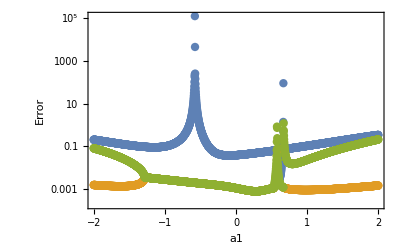

```mathematica
(*The real part of the manifold*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,Manifold[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","Error"}]
```

## Gamma contributions

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

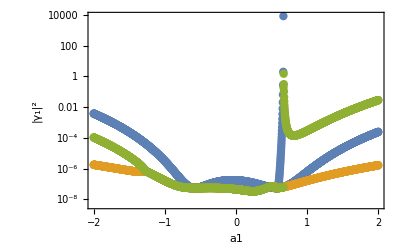

```mathematica
(*Subscript[γ, 1] contribution*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,ManifoldG1[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","|γ_1|^2"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

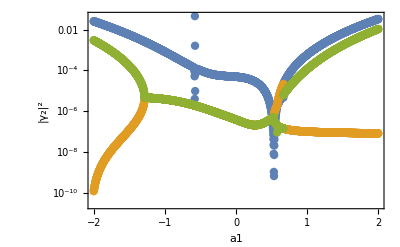

```mathematica
(*Subscript[γ, 2] contribution*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,ManifoldG2[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","|γ_2|^2"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

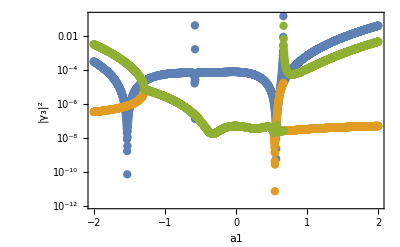

```mathematica
(*Subscript[γ, 3] contribution*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,ManifoldG3[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","|γ_3|^2"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

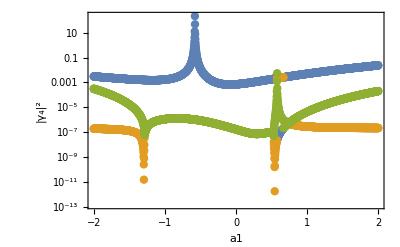

```mathematica
(*Subscript[γ, 4] contribution*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,ManifoldG4[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","|γ_4|^2"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

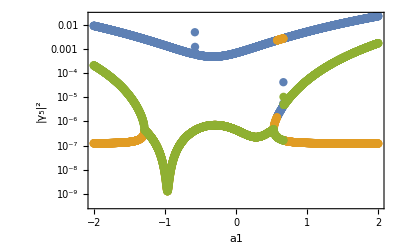

```mathematica
(*Subscript[γ, 5] contribution*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,ManifoldG5[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","|γ_5|^2"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

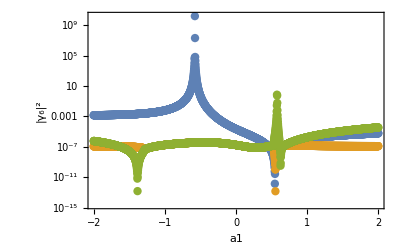

```mathematica
(*Subscript[γ, 6] contribution*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.002]}];
a1vals1=Table[x,{x,Range[0.6678,0.6681,0.000001]}];
a1vals2=Table[x,{x,Range[0.56,0.60,0.0001]}];
a1vals3=Table[x,{x,Range[-0.575,-0.5745,0.00005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,ManifoldG6[a1]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"a1","|γ_6|^2"}]
```

## Imaginary sheet

Visualization of the imaginary part of the manifold

```mathematica
(*Set the range and step*)
reMin=-1;reMax=1;imMin=0;imMax=1;step=0.05;
(*Create lists of real and imaginary parts*)
reVals=Range[reMin,reMax,step];
imVals=Range[imMin,imMax,step];
(*Generate all combinations as complex numbers*)
a1vals=Flatten[Table[x+I y,{x,reVals},{y,imVals}],1];
data=Table[Table[{Re[a1],Im[a1],err},{err,ManifoldLog[a1]}],{a1,a1vals}];
```

$Aborted

```mathematica
ManifoldLog[a1val_?NumericQ]:=Module[{sols,a2val,b1val,Errors={}},
sols=NSolve[{alpha[a1val,a2,b1]==0,beta[a1val,a2,b1]==0},{a2,b1}];
(*Print[sols,"  a1 = ",a1val];*) (*optional debugging*)
(*Loop over all real solutions and compute error for each*)
Do[a2val=a2/. sol;
b1val=b1/. sol;
AppendTo[Errors,
Log10[Sqrt[
Abs[gamma1[a1val,a2val,b1val]]^2+
Abs[gamma2[a1val,a2val,b1val]]^2+
Abs[gamma3[a1val,a2val,b1val]]^2+
Abs[gamma4[a1val,a2val,b1val]]^2+
Abs[gamma5[a1val,a2val,b1val]]^2+
Abs[gamma6[a1val,a2val,b1val]]^2]
]],
{sol,sols}];
(*Print[Length[Errors]]*);
Errors]
```

```mathematica
P1=ListPointPlot3D[data[[;;,1,;;]],PlotStyle->Blue,AxesLabel->{"Re[a1]","Im[a1]","Log10[|Error|]"}];
P2=ListPointPlot3D[data[[;;,2,;;]],PlotStyle->Orange,AxesLabel->{"Re[a1]","Im[a1]","Log10[|Error|]"}];
P3=ListPointPlot3D[data[[;;,3,;;]],PlotStyle->Green,AxesLabel->{"Re[a1]","Im[a1]","Log10[|Error|]"}];
Show[P1,P2,P3]
```

-Graphics3D-